# Clonal Analysis

## Nicholas Wisniewski, Ph.D.

## Blanpain 3 Cell Model “Defining the mode of tumour growth by clonal analysis”

For the code, we have been using the following definitions:

### Type 1

p111 = 0.1: stem → stem + stem
p112 = 0.8: stem → stem+ progenitor 
p122 = 0.1: stem → progenitor + progenitor

lifetime τ_1 = 12 hours

### Type 2

p222 = 0.2: progenitor → progenitor + progenitor
p223 = 0.2: progenitor → progenitor + terminal
p233 = 0.6: progenitor → terminal + terminal

lifetime τ_2 = 48 hours

### Type 3

p33: terminal → terminal

## Initialization

```mathematica
Initialize:=Do[
nrow=25; (* number of rows *)
ncol=25;(* number of columns *)
τ={1,4,∞};(* lifetime of celltypes 0 and 1 *)
state=ConstantArray[0,{nrow,ncol,3}]; (* nrow X ncol X triplet of {celltype, run, time to death} *)
state[[All,All,1]]=0; (* initialize celltype of all cells to terminal *)
state[[13,13,1]]=2;
(*state[[35,35,1]]=1;
state[[65,65,1]]=1;
state[[35,65,1]]=1;
state[[65,35,1]]=1;*)
state[[All,All,2]]=1; (* initialize run# of all cells *)
For[row=1,row≤nrow,row++,
For[col=1,col≤ncol,col++,
Switch[state[[row,col,1]],
0,state[[row,col,3]]=∞,
1,state[[row,col,3]]=RandomVariate[NormalDistribution[τ[[1]],.05]],
2,state[[row,col,3]]=RandomVariate[NormalDistribution[τ[[2]],.05]],
3,state[[row,col,3]]=∞
]]]; (* initialize lifetime of all cells *)
p111=.1;
p112=.8;
p122=.1;
p222=.1;
p223=.8;
p233=.2;
nruns=48; (* number of runs *)
debug=0; (* debug on = 1, off = 0 *)
Life[row_,col_]:=state[[row,col,3]];
Generation[row_,col_]:=state[[row,col,2]];
CellType[row_,col_]:=state[[row,col,1]];
colorset={0->White,1->Green,2->Red,3->Black};
MatrixPlot[state[[All,All,1]],ColorRules->colorset];
state//MatrixForm;
Life[All,All];
,{1}]
```

## Cell growth model

```mathematica
AddCell[where_,oldcell_,newcell_]:=Switch[where,
"North",
state=Insert[state,ConstantArray[0,{ncol,3}],nrow+1]; (* append row on bottom *)
If[debug==1,Print["North, Added Row"];Print[state[[All,All]]//MatrixForm,"nrow=",nrow];MatrixPlot[state[[All,All,1]],ColorRules->colorset]//Print];
For[irow=nrow+1,irow>1,irow--, (* count up from bottom to the top *)
state[[irow,All]]=state[[irow-1,All]] (* slide everything down *)
];
If[debug==1,Print["Slid All Down"]];
currentrow=row+1; (* update row to account for global slide *)
For[irow=1,irow<currentrow,irow++, (* count down from top, to just above current cell *)
state[[irow,col]]=state[[irow+1,col]] (* slide column up, starting at current cell *)
];
newτ=If[newcell≠3,RandomVariate[NormalDistribution[τ[[newcell]],.05]],∞];
oldτ=If[oldcell≠3,RandomVariate[NormalDistribution[τ[[oldcell]],.05]],∞];
state[[currentrow-1,col]]={newcell,run+1,newτ};
state[[currentrow,col]]={oldcell,run+1,oldτ};
If[debug==1,Print["copied, ",{newcell,run+1,newτ},",",{oldcell,run+1,oldτ}]];
nrow++;
(****** need to delete top row here *****)
temp=Drop[state,1];
state=temp;
nrow--,

"East",
state=Transpose[Insert[Transpose[state],ConstantArray[0,{nrow,3}],ncol+1]]; (* append col on right *)
If[debug==1,Print["East, Added Column"];Print[state[[All,All]]//MatrixForm,"ncol=",ncol];MatrixPlot[state[[All,All,1]],ColorRules->colorset]//Print];
For[icol=ncol+1,icol>col,icol--,(* count in from right, to just right of current cell *)
state[[row,icol]]=state[[row,icol-1]] (* slide row right, starting at current cell *)
];
newτ=If[newcell≠3,RandomVariate[NormalDistribution[τ[[newcell]],.05]],∞];
oldτ=If[oldcell≠3,RandomVariate[NormalDistribution[τ[[oldcell]],.05]],∞];
If[debug==1,Print["copied, ",{oldcell,run+1,oldτ},",",{newcell,run+1,newτ}]];
state[[row,col]]={oldcell,run+1,oldτ}; (* update run, decrement lifetime *) 
state[[row,col+1]]={newcell,run+1,newτ}; (* update new cell *)
ncol++;
(****** need to delete right column here *****)
temp=Drop[state,{},-1];
state=temp;
ncol--,

"South",
state=Insert[state,ConstantArray[0,{ncol,3}],nrow+1]; (* append row on bottom *)
If[debug==1,Print["South, Added Row"];Print[state[[All,All]]//MatrixForm,"nrow=",nrow];MatrixPlot[state[[All,All,1]],ColorRules->colorset]//Print];
For[irow=nrow+1,irow>row,irow--, (* count up from bottom, to just below current cell *)
state[[irow,col]]=state[[irow-1,col]] (* slide column down, starting at current cell *)
];
newτ=If[newcell≠3,RandomVariate[NormalDistribution[τ[[newcell]],.05]],∞];
oldτ=If[oldcell≠3,RandomVariate[NormalDistribution[τ[[oldcell]],.05]],∞];
If[debug==1,Print["copied, ",{oldcell,run+1,oldτ},",",{newcell,run+1,newτ}]];
state[[row,col]]={oldcell,run+1,oldτ};
state[[row+1,col]]={newcell,run+1,newτ};
nrow++;
(****** need to delete bottom row here *****)
temp=Drop[state,-1];
state=temp;
nrow--,

"West",
state=Transpose[Insert[Transpose[state],ConstantArray[0,{nrow,3}],ncol+1]]; (* append col on right *)
If[debug==1,Print["West, Added Column"];Print[state[[All,All]]//MatrixForm,"ncol=",ncol];MatrixPlot[state[[All,All,1]],ColorRules->colorset]//Print];
For[icol=ncol+1,icol>1,icol--, (* count in from right to the left *)
state[[All,icol]]=state[[All,icol-1]] (* slide everything right *)
];
newτ=If[newcell≠3,RandomVariate[NormalDistribution[τ[[newcell]],.05]],∞];
oldτ=If[oldcell≠3,RandomVariate[NormalDistribution[τ[[oldcell]],.05]],∞];
currentcol=col+1; (* update col to account for global slide *)
For[icol=1,icol<currentcol,icol++, (* count in from left, to just left of current cell *)
state[[row,icol]]=state[[row,icol+1]] (* slide row left, starting at current cell *)
];
If[debug==1,Print["copied, ",{newcell,run+1,newτ},",",{oldcell,run+1,oldτ}]];
state[[row,currentcol-1]]={newcell,run+1,newτ};
state[[row,currentcol]]={oldcell,run+1,oldτ};
ncol++;
(****** need to delete left column here *****)
temp=Drop[state,{},1];
state=temp;
ncol--
];
```

## Progenitor Simulation (80% ⇒ n=800)

#### Small Canvas

```mathematica
Initialize:=Do[
nrow=25; (* number of rows *)
ncol=25;(* number of columns *)
τ={1,4,∞};(* lifetime of celltypes 0 and 1 *)
state=ConstantArray[0,{nrow,ncol,3}]; (* nrow X ncol X triplet of {celltype, run, time to death} *)
state[[All,All,1]]=0; (* initialize celltype of all cells to terminal *)
state[[13,13,1]]=2;
(*state[[35,35,1]]=1;
state[[65,65,1]]=1;
state[[35,65,1]]=1;
state[[65,35,1]]=1;*)
state[[All,All,2]]=1; (* initialize run# of all cells *)
For[row=1,row≤nrow,row++,
For[col=1,col≤ncol,col++,
Switch[state[[row,col,1]],
0,state[[row,col,3]]=∞,
1,state[[row,col,3]]=RandomVariate[NormalDistribution[τ[[1]],.05]],
2,state[[row,col,3]]=RandomVariate[NormalDistribution[τ[[2]],.05]],
3,state[[row,col,3]]=∞
]]]; (* initialize lifetime of all cells *)
p111=.2;
p112=.6;
p122=.2;
p222=.1;
p223=.8;
p233=.1;
nruns=48; (* number of runs *)
debug=0; (* debug on = 1, off = 0 *)
Life[row_,col_]:=state[[row,col,3]];
Generation[row_,col_]:=state[[row,col,2]];
CellType[row_,col_]:=state[[row,col,1]];
colorset={0->White,1->Green,2->Red,3->Black};
MatrixPlot[state[[All,All,1]],ColorRules->colorset];
state//MatrixForm;
Life[All,All];
,{1}]
```

Instance 1

Instance 2

Instance 3

Instance 4

Instance 5

Instance 6

Instance 7

Instance 8

Instance 9

Instance 10

Instance 11

Instance 12

Instance 13

Instance 14

Instance 15

Instance 16

Instance 17

Instance 18

Instance 19

Instance 20

Instance 21

Instance 22

Instance 23

Instance 24

Instance 25

Instance 26

Instance 27

Instance 28

Instance 29

Instance 30

Instance 31

Instance 32

Instance 33

Instance 34

Instance 35

Instance 36

Instance 37

Instance 38

Instance 39

Instance 40

Instance 41

Instance 42

Instance 43

Instance 44

Instance 45

Instance 46

Instance 47

Instance 48

Instance 49

Instance 50

Instance 51

Instance 52

Instance 53

Instance 54

Instance 55

Instance 56

Instance 57

Instance 58

Instance 59

Instance 60

Instance 61

Instance 62

Instance 63

Instance 64

Instance 65

Instance 66

Instance 67

Instance 68

Instance 69

Instance 70

Instance 71

Instance 72

Instance 73

Instance 74

Instance 75

Instance 76

Instance 77

Instance 78

Instance 79

Instance 80

Instance 81

Instance 82

Instance 83

Instance 84

Instance 85

Instance 86

Instance 87

Instance 88

Instance 89

Instance 90

Instance 91

Instance 92

Instance 93

Instance 94

Instance 95

Instance 96

Instance 97

Instance 98

Instance 99

Instance 100

Instance 101

Instance 102

Instance 103

Instance 104

Instance 105

Instance 106

Instance 107

Instance 108

Instance 109

Instance 110

Instance 111

Instance 112

Instance 113

Instance 114

Instance 115

Instance 116

Instance 117

Instance 118

Instance 119

Instance 120

Instance 121

Instance 122

Instance 123

Instance 124

Instance 125

Instance 126

Instance 127

Instance 128

Instance 129

Instance 130

Instance 131

Instance 132

Instance 133

Instance 134

Instance 135

Instance 136

Instance 137

Instance 138

Instance 139

Instance 140

Instance 141

Instance 142

Instance 143

Instance 144

Instance 145

Instance 146

Instance 147

Instance 148

Instance 149

Instance 150

Instance 151

Instance 152

Instance 153

Instance 154

Instance 155

Instance 156

Instance 157

Instance 158

Instance 159

Instance 160

Instance 161

Instance 162

Instance 163

Instance 164

Instance 165

Instance 166

Instance 167

Instance 168

Instance 169

Instance 170

Instance 171

Instance 172

Instance 173

Instance 174

Instance 175

Instance 176

Instance 177

Instance 178

Instance 179

Instance 180

Instance 181

Instance 182

Instance 183

Instance 184

Instance 185

Instance 186

Instance 187

Instance 188

Instance 189

Instance 190

Instance 191

Instance 192

Instance 193

Instance 194

Instance 195

Instance 196

Instance 197

Instance 198

Instance 199

Instance 200

Instance 201

Instance 202

Instance 203

Instance 204

Instance 205

Instance 206

Instance 207

Instance 208

Instance 209

Instance 210

Instance 211

Instance 212

Instance 213

Instance 214

Instance 215

Instance 216

Instance 217

Instance 218

Instance 219

Instance 220

Instance 221

Instance 222

Instance 223

Instance 224

Instance 225

Instance 226

Instance 227

Instance 228

Instance 229

Instance 230

Instance 231

Instance 232

Instance 233

Instance 234

Instance 235

Instance 236

Instance 237

Instance 238

Instance 239

Instance 240

Instance 241

Instance 242

Instance 243

Instance 244

Instance 245

Instance 246

Instance 247

Instance 248

Instance 249

Instance 250

Instance 251

Instance 252

Instance 253

Instance 254

Instance 255

Instance 256

Instance 257

Instance 258

Instance 259

Instance 260

Instance 261

Instance 262

Instance 263

Instance 264

Instance 265

Instance 266

Instance 267

Instance 268

Instance 269

Instance 270

Instance 271

Instance 272

Instance 273

Instance 274

Instance 275

Instance 276

Instance 277

Instance 278

Instance 279

Instance 280

Instance 281

Instance 282

Instance 283

Instance 284

Instance 285

Instance 286

Instance 287

Instance 288

Instance 289

Instance 290

Instance 291

Instance 292

Instance 293

Instance 294

Instance 295

Instance 296

Instance 297

Instance 298

Instance 299

Instance 300

Instance 301

Instance 302

Instance 303

Instance 304

Instance 305

Instance 306

Instance 307

Instance 308

Instance 309

Instance 310

Instance 311

Instance 312

Instance 313

Instance 314

Instance 315

Instance 316

Instance 317

Instance 318

Instance 319

Instance 320

Instance 321

Instance 322

Instance 323

Instance 324

Instance 325

Instance 326

Instance 327

Instance 328

Instance 329

Instance 330

Instance 331

Instance 332

Instance 333

Instance 334

Instance 335

Instance 336

Instance 337

Instance 338

Instance 339

Instance 340

Instance 341

Instance 342

Instance 343

Instance 344

Instance 345

Instance 346

Instance 347

Instance 348

Instance 349

Instance 350

Instance 351

Instance 352

Instance 353

Instance 354

Instance 355

Instance 356

Instance 357

Instance 358

Instance 359

Instance 360

Instance 361

Instance 362

Instance 363

Instance 364

Instance 365

Instance 366

Instance 367

Instance 368

Instance 369

Instance 370

Instance 371

Instance 372

Instance 373

Instance 374

Instance 375

Instance 376

Instance 377

Instance 378

Instance 379

Instance 380

Instance 381

Instance 382

Instance 383

Instance 384

Instance 385

Instance 386

Instance 387

Instance 388

Instance 389

Instance 390

Instance 391

Instance 392

Instance 393

Instance 394

Instance 395

Instance 396

Instance 397

Instance 398

Instance 399

Instance 400

Instance 401

Instance 402

Instance 403

Instance 404

Instance 405

Instance 406

Instance 407

Instance 408

Instance 409

Instance 410

Instance 411

Instance 412

Instance 413

Instance 414

Instance 415

Instance 416

Instance 417

Instance 418

Instance 419

Instance 420

Instance 421

Instance 422

Instance 423

Instance 424

Instance 425

Instance 426

Instance 427

Instance 428

Instance 429

Instance 430

Instance 431

Instance 432

Instance 433

Instance 434

Instance 435

Instance 436

Instance 437

Instance 438

Instance 439

Instance 440

Instance 441

Instance 442

Instance 443

Instance 444

Instance 445

Instance 446

Instance 447

Instance 448

Instance 449

Instance 450

Instance 451

Instance 452

Instance 453

Instance 454

Instance 455

Instance 456

Instance 457

Instance 458

Instance 459

Instance 460

Instance 461

Instance 462

Instance 463

Instance 464

Instance 465

Instance 466

Instance 467

Instance 468

Instance 469

Instance 470

Instance 471

Instance 472

Instance 473

Instance 474

Instance 475

Instance 476

Instance 477

Instance 478

Instance 479

Instance 480

Instance 481

Instance 482

Instance 483

Instance 484

Instance 485

Instance 486

Instance 487

Instance 488

Instance 489

Instance 490

Instance 491

Instance 492

Instance 493

Instance 494

Instance 495

Instance 496

Instance 497

Instance 498

Instance 499

Instance 500

Instance 501

Instance 502

Instance 503

Instance 504

Instance 505

Instance 506

Instance 507

Instance 508

Instance 509

Instance 510

Instance 511

Instance 512

Instance 513

Instance 514

Instance 515

Instance 516

Instance 517

Instance 518

Instance 519

Instance 520

Instance 521

Instance 522

Instance 523

Instance 524

Instance 525

Instance 526

Instance 527

Instance 528

Instance 529

Instance 530

Instance 531

Instance 532

Instance 533

Instance 534

Instance 535

Instance 536

Instance 537

Instance 538

Instance 539

Instance 540

Instance 541

Instance 542

Instance 543

Instance 544

Instance 545

Instance 546

Instance 547

Instance 548

Instance 549

Instance 550

Instance 551

Instance 552

Instance 553

Instance 554

Instance 555

Instance 556

Instance 557

Instance 558

Instance 559

Instance 560

Instance 561

Instance 562

Instance 563

Instance 564

Instance 565

Instance 566

Instance 567

Instance 568

Instance 569

Instance 570

Instance 571

Instance 572

Instance 573

Instance 574

Instance 575

Instance 576

Instance 577

Instance 578

Instance 579

Instance 580

Instance 581

Instance 582

Instance 583

Instance 584

Instance 585

Instance 586

Instance 587

Instance 588

Instance 589

Instance 590

Instance 591

Instance 592

Instance 593

Instance 594

Instance 595

Instance 596

Instance 597

Instance 598

Instance 599

Instance 600

Instance 601

Instance 602

Instance 603

Instance 604

Instance 605

Instance 606

Instance 607

Instance 608

Instance 609

Instance 610

Instance 611

Instance 612

Instance 613

Instance 614

Instance 615

Instance 616

Instance 617

Instance 618

Instance 619

Instance 620

Instance 621

Instance 622

Instance 623

Instance 624

Instance 625

Instance 626

Instance 627

Instance 628

Instance 629

Instance 630

Instance 631

Instance 632

Instance 633

Instance 634

Instance 635

Instance 636

Instance 637

Instance 638

Instance 639

Instance 640

Instance 641

Instance 642

Instance 643

Instance 644

Instance 645

Instance 646

Instance 647

Instance 648

Instance 649

Instance 650

Instance 651

Instance 652

Instance 653

Instance 654

Instance 655

Instance 656

Instance 657

Instance 658

Instance 659

Instance 660

Instance 661

Instance 662

Instance 663

Instance 664

Instance 665

Instance 666

Instance 667

Instance 668

Instance 669

Instance 670

Instance 671

Instance 672

Instance 673

Instance 674

Instance 675

Instance 676

Instance 677

Instance 678

Instance 679

Instance 680

Instance 681

Instance 682

Instance 683

Instance 684

Instance 685

Instance 686

Instance 687

Instance 688

Instance 689

Instance 690

Instance 691

Instance 692

Instance 693

Instance 694

Instance 695

Instance 696

Instance 697

Instance 698

Instance 699

Instance 700

Instance 701

Instance 702

Instance 703

Instance 704

Instance 705

Instance 706

Instance 707

Instance 708

Instance 709

Instance 710

Instance 711

Instance 712

Instance 713

Instance 714

Instance 715

Instance 716

Instance 717

Instance 718

Instance 719

Instance 720

Instance 721

Instance 722

Instance 723

Instance 724

Instance 725

Instance 726

Instance 727

Instance 728

Instance 729

Instance 730

Instance 731

Instance 732

Instance 733

Instance 734

Instance 735

Instance 736

Instance 737

Instance 738

Instance 739

Instance 740

Instance 741

Instance 742

Instance 743

Instance 744

Instance 745

Instance 746

Instance 747

Instance 748

Instance 749

Instance 750

Instance 751

Instance 752

Instance 753

Instance 754

Instance 755

Instance 756

Instance 757

Instance 758

Instance 759

Instance 760

Instance 761

Instance 762

Instance 763

Instance 764

Instance 765

Instance 766

Instance 767

Instance 768

Instance 769

Instance 770

Instance 771

Instance 772

Instance 773

Instance 774

Instance 775

Instance 776

Instance 777

Instance 778

Instance 779

Instance 780

Instance 781

Instance 782

Instance 783

Instance 784

Instance 785

Instance 786

Instance 787

Instance 788

Instance 789

Instance 790

Instance 791

Instance 792

Instance 793

Instance 794

Instance 795

Instance 796

Instance 797

Instance 798

Instance 799

Instance 800

Analysis of all Instances:

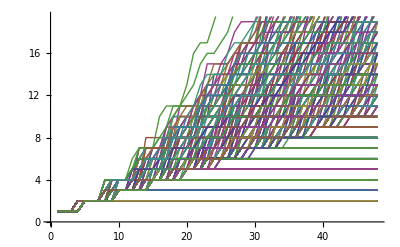

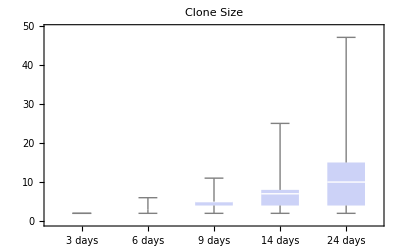

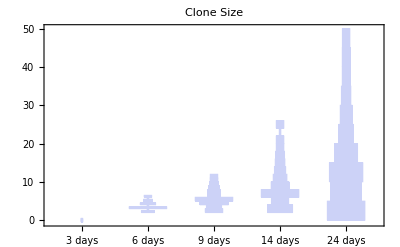

```mathematica
DOnumber=800;
donum=1;
totalcellssuper={};
Do[
Initialize;
rawoutput={};
output={};
cellcount={};
If[debug==1,Print[state[[All,All]]//MatrixForm]];
(*MatrixPlot[state[[All,All,1]],ColorRules->colorset]*)
For[run=1,run≤nruns,run++,(* index over each run/generation *)
nrow=Dimensions[state][[1]]; (* check max number of rows *)
ncol=Dimensions[state][[2]]; (* check max number of cols *)
For[row=1,row≤nrow,row++, (* index over each row *)
For[col=1,col≤ncol,col++, (* index over each column *)
(*If[debug==1,Print["run=",run,",","row=",row,",","col=",col,","]];*)
If[Generation[row,col]==run ,state[[row,col,3]]=Life[row,col]-1]; (* degrade lifetime if on current run *)
(*Print[state[[row,col,3]]];*)
If[Generation[row,col]==run ∧ Life[row,col]≤0,(* If clock is synched to this run AND its life has run out *)
Switch[CellType[row,col],(* Switch on celltype *)
1,
If[debug==1,Print["CellType=",CellType[row,col]]];
uniform=RandomReal[]; (* pick a number in [0,1] from a uniform distribution. this is how we make decisions *)
direction=RandomInteger[3]/.{0->"North",1->"East",2->"South",3->"West"}; 

If[debug==1,Print["uni=",uniform,",","dir=",direction,",","Gen=",Generation[row,col],",","Life=", Life[row,col]]];
If[uniform>(p111+p112),AddCell[direction,2,2],If[uniform>p111,AddCell[direction,1,2],AddCell[direction,1,1]]]; 
(*depricate If[uniform>p11,AddCell[direction,1,2],AddCell[direction,1,1]]; *)
If[debug==1,Print["Added Cell"];MatrixPlot[state[[All,All,1]],ColorRules->colorset]//Print;Print[state[[All,All]]//MatrixForm]], 
(* back to Switch on celltype *)
2,
If[debug==1,Print["CellType=",CellType[row,col]]];
uniform=RandomReal[]; (* pick a number in [0,1] from a uniform distribution. this is how we make decisions *)
direction=RandomInteger[3]/.{0->"North",1->"East",2->"South",3->"West"}; 

If[debug==1,Print["uni=",uniform,",","dir=",direction,",","Gen=",Generation[row,col],",","Life=", Life[row,col]]];
If[uniform>(p222+p223),AddCell[direction,3,3],If[uniform>p222,AddCell[direction,2,3],AddCell[direction,2,2]]]; 
(*depricate If[uniform>p22,AddCell[direction,2,3],AddCell[direction,2,2]]; *)
If[debug==1,Print["Added Cell"];MatrixPlot[state[[All,All,1]],ColorRules->colorset]//Print;Print[state[[All,All]]//MatrixForm]],
(* Back to Switch on celltype *)
3,
If[debug==1,Print["CellType=",CellType[row,col]]];
state[[row,col]]={3,run+1,state[[row,col,3]]}(* update the old cell *)
] (* end Switch celltype *)
] (* end if[run∧life] with no elses *)
If[state[[row,col,2]]==run,state[[row,col,2]]++ ](*increment run*)
] (* end for column *)(* Apply update rules. If[expr==TRUE, then do, else do] *)
]; (* end for row *) 
(*temp=Drop[state,{},Position[Table[Total[state[[All,colm,1]]],{colm,1,Dimensions[state][[2]]}],0][[1,1]]-ncol-1];
temp2=Drop[temp,Position[Table[Total[state[[r,All,1]]],{r,1,Dimensions[state][[1]]}],0][[1,1]]-nrow-1];
state=.;
state=temp2;
(*MatrixPlot[temp2[[All,All,1]]];*)
*)
label=StringJoin[ToString[run*12]," hrs"];
AppendTo[rawoutput,state[[All,All,1]]];
AppendTo[cellcount,Total[Mod[rawoutput[[-1]],2],2]];
AppendTo[output,Graphics[MatrixPlot[state[[All,All,1]],ColorRules->colorset,PlotLabel->label]]];
(*Print[state[[All,All]]//MatrixForm];*)
If[debug==1,Print[state[[All,All,1]]//MatrixForm]];
(*Print[run+1];*)
](* end for runs *)
Print["Instance ",donum];
donum++;
(*Print[output[[Round[{3,6,9,14,24}*24/12]]]]; (* print only days {3,6,9,14,24} *)*)
totalcells=Table[Count[rawoutput[[i]],Except[0],2]-nrow,{i,1,Length[rawoutput]}]; (* count total cells from initial condition *)
(*ListLinePlot[totalcells,PlotRange->All,Frame->Automatic,FrameLabel->{"generation","total cells"}]//Print; (* plot growth for each DO *)*)
AppendTo[totalcellssuper,totalcells];, (* make outer collection of growth numbers *)
{DOnumber}]; (* Number of times to DO *)
Print["Analysis of all Instances:"];
ListLinePlot[totalcellssuper,Frame->Automatic,FrameLabel->{"generation","total cells"}] (* plot all growths *)
frames=Round[{3,6,9,14,24}*24/12];
BoxWhiskerChart[Table[totalcellssuper[[All,frames[[i]]]],{i,1,Length[frames]}],ChartLabels->{"3 days","6 days","9 days","14 days","24 days"},PlotLabel->"Clone Size"] 
DistributionChart[Table[totalcellssuper[[All,frames[[i]]]],{i,1,Length[frames]}],ChartElementFunction->"HistogramDensity",ChartLabels->{"3 days","6 days","9 days","14 days","24 days"},PlotLabel->"Clone Size"] (* plot box and whiskers *)
```

```mathematica
progenitors=totalcellssuper;
```

```mathematica
Table[totalcellssuper[[All,frames[[i]]]],{i,1,Length[frames]}]
```

## Stem Simulation (20% ⇒ n=200)

#### Small Canvas

```mathematica
Initialize:=Do[
nrow=50; (* number of rows *)
ncol=50;(* number of columns *)
τ={1,4,∞};(* lifetime of celltypes 0 and 1 *)
state=ConstantArray[0,{nrow,ncol,3}]; (* nrow X ncol X triplet of {celltype, run, time to death} *)
state[[All,All,1]]=0; (* initialize celltype of all cells to terminal *)
state[[25,25,1]]=1;
(*state[[35,35,1]]=1;
state[[65,65,1]]=1;
state[[35,65,1]]=1;
state[[65,35,1]]=1;*)
state[[All,All,2]]=1; (* initialize run# of all cells *)
For[row=1,row≤nrow,row++,
For[col=1,col≤ncol,col++,
Switch[state[[row,col,1]],
0,state[[row,col,3]]=∞,
1,state[[row,col,3]]=RandomVariate[NormalDistribution[τ[[1]],.05]],
2,state[[row,col,3]]=RandomVariate[NormalDistribution[τ[[2]],.05]],
3,state[[row,col,3]]=∞
]]]; (* initialize lifetime of all cells *)
p111=.2;
p112=.6;
p122=.2;
p222=.1;
p223=.8;
p233=.1;
nruns=48; (* number of runs *)
debug=0; (* debug on = 1, off = 0 *)
Life[row_,col_]:=state[[row,col,3]];
Generation[row_,col_]:=state[[row,col,2]];
CellType[row_,col_]:=state[[row,col,1]];
colorset={0->White,1->Green,2->Red,3->Black};
MatrixPlot[state[[All,All,1]],ColorRules->colorset];
state//MatrixForm;
Life[All,All];
,{1}]
```

Instance 1

Instance 2

Instance 3

Instance 4

Instance 5

Instance 6

Instance 7

Instance 8

Instance 9

Instance 10

Instance 11

Instance 12

Instance 13

Instance 14

Instance 15

Instance 16

Instance 17

Instance 18

Instance 19

Instance 20

Instance 21

Instance 22

Instance 23

Instance 24

Instance 25

Instance 26

Instance 27

Instance 28

Instance 29

Instance 30

Instance 31

Instance 32

Instance 33

Instance 34

Instance 35

Instance 36

Instance 37

Instance 38

Instance 39

Instance 40

Instance 41

Instance 42

Instance 43

Instance 44

Instance 45

Instance 46

Instance 47

Instance 48

Instance 49

Instance 50

Instance 51

Instance 52

Instance 53

Instance 54

Instance 55

Instance 56

Instance 57

Instance 58

Instance 59

Instance 60

Instance 61

Instance 62

Instance 63

Instance 64

Instance 65

Instance 66

Instance 67

Instance 68

Instance 69

Instance 70

Instance 71

Instance 72

Instance 73

Instance 74

Instance 75

Instance 76

Instance 77

Instance 78

Instance 79

Instance 80

Instance 81

Instance 82

Instance 83

Instance 84

Instance 85

Instance 86

Instance 87

Instance 88

Instance 89

Instance 90

Instance 91

Instance 92

Instance 93

Instance 94

Instance 95

Instance 96

Instance 97

Instance 98

Instance 99

Instance 100

Instance 101

Instance 102

Instance 103

Instance 104

Instance 105

Instance 106

Instance 107

Instance 108

Instance 109

Instance 110

Instance 111

Instance 112

Instance 113

Instance 114

Instance 115

Instance 116

Instance 117

Instance 118

Instance 119

Instance 120

Instance 121

Instance 122

Instance 123

Instance 124

Instance 125

Instance 126

Instance 127

Instance 128

Instance 129

Instance 130

Instance 131

Instance 132

Instance 133

Instance 134

Instance 135

Instance 136

Instance 137

Instance 138

Instance 139

Instance 140

Instance 141

Instance 142

Instance 143

Instance 144

Instance 145

Instance 146

Instance 147

Instance 148

Instance 149

Instance 150

Instance 151

Instance 152

Instance 153

Instance 154

Instance 155

Instance 156

Instance 157

Instance 158

Instance 159

Instance 160

Instance 161

Instance 162

Instance 163

Instance 164

Instance 165

Instance 166

Instance 167

Instance 168

Instance 169

Instance 170

Instance 171

Instance 172

Instance 173

Instance 174

Instance 175

Instance 176

Instance 177

Instance 178

Instance 179

Instance 180

Instance 181

Instance 182

Instance 183

Instance 184

Instance 185

Instance 186

Instance 187

Instance 188

Instance 189

Instance 190

Instance 191

Instance 192

Instance 193

Instance 194

Instance 195

Instance 196

Instance 197

Instance 198

Instance 199

Instance 200

Analysis of all Instances:

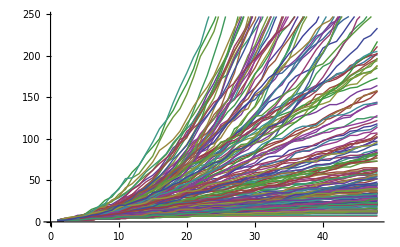

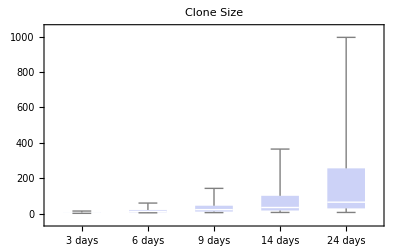

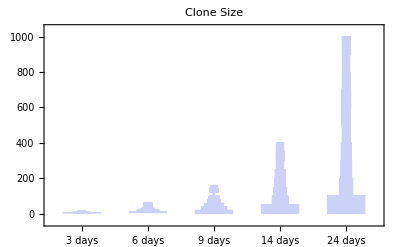

```mathematica
DOnumber=200;
donum=1;
totalcellssuper={};
Do[
Initialize;
rawoutput={};
output={};
cellcount={};
If[debug==1,Print[state[[All,All]]//MatrixForm]];
(*MatrixPlot[state[[All,All,1]],ColorRules->colorset]*)
For[run=1,run≤nruns,run++,(* index over each run/generation *)
nrow=Dimensions[state][[1]]; (* check max number of rows *)
ncol=Dimensions[state][[2]]; (* check max number of cols *)
For[row=1,row≤nrow,row++, (* index over each row *)
For[col=1,col≤ncol,col++, (* index over each column *)
(*If[debug==1,Print["run=",run,",","row=",row,",","col=",col,","]];*)
If[Generation[row,col]==run ,state[[row,col,3]]=Life[row,col]-1]; (* degrade lifetime if on current run *)
(*Print[state[[row,col,3]]];*)
If[Generation[row,col]==run ∧ Life[row,col]≤0,(* If clock is synched to this run AND its life has run out *)
Switch[CellType[row,col],(* Switch on celltype *)
1,
If[debug==1,Print["CellType=",CellType[row,col]]];
uniform=RandomReal[]; (* pick a number in [0,1] from a uniform distribution. this is how we make decisions *)
direction=RandomInteger[3]/.{0->"North",1->"East",2->"South",3->"West"}; 

If[debug==1,Print["uni=",uniform,",","dir=",direction,",","Gen=",Generation[row,col],",","Life=", Life[row,col]]];
If[uniform>(p111+p112),AddCell[direction,2,2],If[uniform>p111,AddCell[direction,1,2],AddCell[direction,1,1]]]; 
(*depricate If[uniform>p11,AddCell[direction,1,2],AddCell[direction,1,1]]; *)
If[debug==1,Print["Added Cell"];MatrixPlot[state[[All,All,1]],ColorRules->colorset]//Print;Print[state[[All,All]]//MatrixForm]], 
(* back to Switch on celltype *)
2,
If[debug==1,Print["CellType=",CellType[row,col]]];
uniform=RandomReal[]; (* pick a number in [0,1] from a uniform distribution. this is how we make decisions *)
direction=RandomInteger[3]/.{0->"North",1->"East",2->"South",3->"West"}; 

If[debug==1,Print["uni=",uniform,",","dir=",direction,",","Gen=",Generation[row,col],",","Life=", Life[row,col]]];
If[uniform>(p222+p223),AddCell[direction,3,3],If[uniform>p222,AddCell[direction,2,3],AddCell[direction,2,2]]]; 
(*depricate If[uniform>p22,AddCell[direction,2,3],AddCell[direction,2,2]]; *)
If[debug==1,Print["Added Cell"];MatrixPlot[state[[All,All,1]],ColorRules->colorset]//Print;Print[state[[All,All]]//MatrixForm]],
(* Back to Switch on celltype *)
3,
If[debug==1,Print["CellType=",CellType[row,col]]];
state[[row,col]]={3,run+1,state[[row,col,3]]}(* update the old cell *)
] (* end Switch celltype *)
] (* end if[run∧life] with no elses *)
If[state[[row,col,2]]==run,state[[row,col,2]]++ ](*increment run*)
] (* end for column *)(* Apply update rules. If[expr==TRUE, then do, else do] *)
]; (* end for row *) 
(*temp=Drop[state,{},Position[Table[Total[state[[All,colm,1]]],{colm,1,Dimensions[state][[2]]}],0][[1,1]]-ncol-1];
temp2=Drop[temp,Position[Table[Total[state[[r,All,1]]],{r,1,Dimensions[state][[1]]}],0][[1,1]]-nrow-1];
state=.;
state=temp2;
(*MatrixPlot[temp2[[All,All,1]]];*)
*)
label=StringJoin[ToString[run*12]," hrs"];
AppendTo[rawoutput,state[[All,All,1]]];
AppendTo[cellcount,Total[Mod[rawoutput[[-1]],2],2]];
AppendTo[output,Graphics[MatrixPlot[state[[All,All,1]],ColorRules->colorset,PlotLabel->label]]];
(*Print[state[[All,All]]//MatrixForm];*)
If[debug==1,Print[state[[All,All,1]]//MatrixForm]];
(*Print[run+1];*)
](* end for runs *)
Print["Instance ",donum];
donum++;
(*Print[output[[Round[{3,6,9,14,24}*24/12]]]]; (* print only days {3,6,9,14,24} *)*)
totalcells=Table[Count[rawoutput[[i]],Except[0],2]-nrow,{i,1,Length[rawoutput]}]; (* count total cells from initial condition *)
(*ListLinePlot[totalcells,PlotRange->All,Frame->Automatic,FrameLabel->{"generation","total cells"}]//Print; (* plot growth for each DO *)*)
AppendTo[totalcellssuper,totalcells];, (* make outer collection of growth numbers *)
{DOnumber}]; (* Number of times to DO *)
Print["Analysis of all Instances:"];
ListLinePlot[totalcellssuper,Frame->Automatic,FrameLabel->{"generation","total cells"}] (* plot all growths *)
frames=Round[{3,6,9,14,24}*24/12];
BoxWhiskerChart[Table[totalcellssuper[[All,frames[[i]]]],{i,1,Length[frames]}],ChartLabels->{"3 days","6 days","9 days","14 days","24 days"},PlotLabel->"Clone Size"] 
DistributionChart[Table[totalcellssuper[[All,frames[[i]]]],{i,1,Length[frames]}],ChartElementFunction->"HistogramDensity",ChartLabels->{"3 days","6 days","9 days","14 days","24 days"},PlotLabel->"Clone Size"] (* plot box and whiskers *)
```

```mathematica
stems=totalcellssuper;
```

## Save and Import Data

```mathematica
filename="~/Desktop/blanpain2618";
```

```mathematica
DumpSave[filename,"Global`"];
```

```mathematica
Import[filename]
```

## Merge Analysis

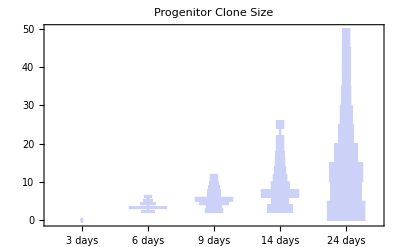

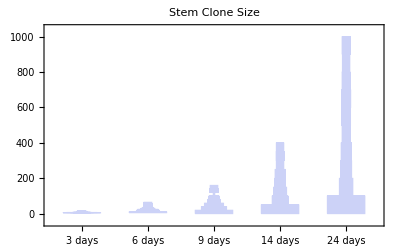

```mathematica
DistributionChart[Table[progenitors[[All,frames[[i]]]],{i,1,Length[frames]}],ChartElementFunction->"HistogramDensity",ChartLabels->{"3 days","6 days","9 days","14 days","24 days"},PlotLabel->"Progenitor Clone Size"] 
DistributionChart[Table[stems[[All,frames[[i]]]],{i,1,Length[frames]}],ChartElementFunction->"HistogramDensity",ChartLabels->{"3 days","6 days","9 days","14 days","24 days"},PlotLabel->"Stem Clone Size"]
```

```mathematica
allcells=Join[stems,progenitors];
```

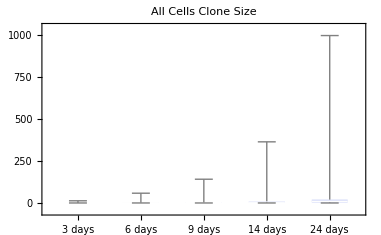

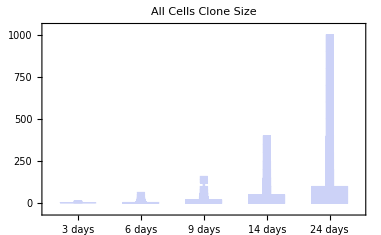

```mathematica
BoxWhiskerChart[Table[allcells[[All,frames[[i]]]],{i,1,Length[frames]}],ChartLabels->{"3 days","6 days","9 days","14 days","24 days"},PlotLabel->"All Cells Clone Size"] 
DistributionChart[Table[allcells[[All,frames[[i]]]],{i,1,Length[frames]}],ChartElementFunction->"HistogramDensity",ChartLabels->{"3 days","6 days","9 days","14 days","24 days"},PlotLabel->"All Cells Clone Size"]
```

```mathematica
cumulative=Table[Length[Select[allcells[[All,frames[[j]]]],#>=i&]]/10//N,{j,1,Length[frames]},{i,1,50}];
```

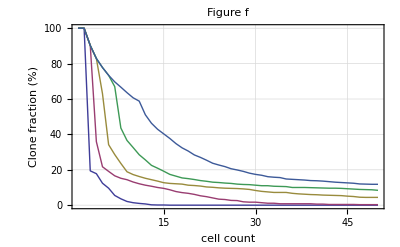

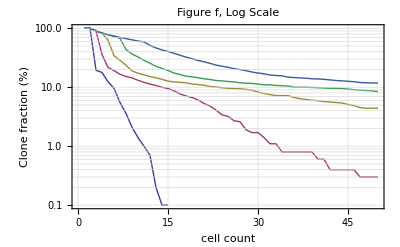

```mathematica
ListLinePlot[cumulative,PlotRange->All,PlotLabel->"Figure f",Frame->True,GridLines->Automatic,FrameLabel->{"cell count","Clone fraction (%)"}]
ListLogPlot[cumulative,PlotRange->All,Joined->True,PlotLabel->"Figure f, Log Scale",GridLines->Automatic,Frame->True,FrameLabel->{"cell count","Clone fraction (%)"}]
```

### With Singlets

```mathematica
singlets=ConstantArray[1,{4000,48}];
```

```mathematica
allcellssinglets=Join[stems,progenitors,singlets];
```

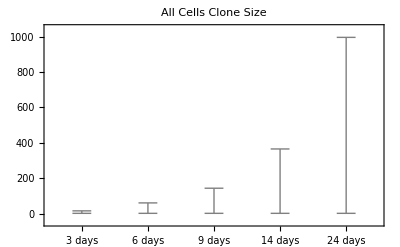

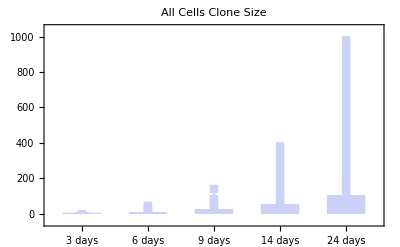

```mathematica
BoxWhiskerChart[Table[allcellssinglets[[All,frames[[i]]]],{i,1,Length[frames]}],ChartLabels->{"3 days","6 days","9 days","14 days","24 days"},PlotLabel->"All Cells Clone Size"] 
DistributionChart[Table[allcellssinglets[[All,frames[[i]]]],{i,1,Length[frames]}],ChartElementFunction->"HistogramDensity",ChartLabels->{"3 days","6 days","9 days","14 days","24 days"},PlotLabel->"All Cells Clone Size"]
```

```mathematica
cumulativewithsinglets=Table[Length[Select[allcellssinglets[[All,frames[[j]]]],#>=i&]]/(Dimensions[allcellssinglets][[1]]/100)//N,{j,1,Length[frames]},{i,1,50}];
```

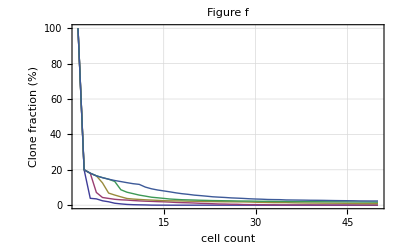

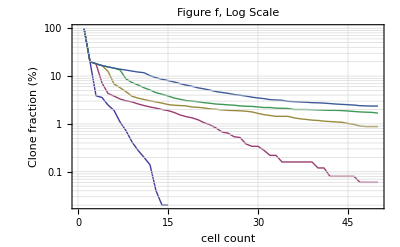

```mathematica
ListLinePlot[cumulativewithsinglets,PlotRange->All,PlotLabel->"Figure f",Frame->True,GridLines->Automatic,FrameLabel->{"cell count","Clone fraction (%)"}]
ListLogPlot[cumulativewithsinglets,PlotRange->All,Joined->True,PlotLabel->"Figure f, Log Scale",GridLines->Automatic,Frame->True,FrameLabel->{"cell count","Clone fraction (%)"}]
```

### Cumulative with 2D correction

```mathematica
cumulativewithsinglets2D=Table[Length[Select[Round[Sqrt[3*allcellssinglets[[All,frames[[j]]]]]],#>=i&]]/(Dimensions[allcellssinglets][[1]]/100)//N,{j,1,Length[frames]},{i,1,50}];
```

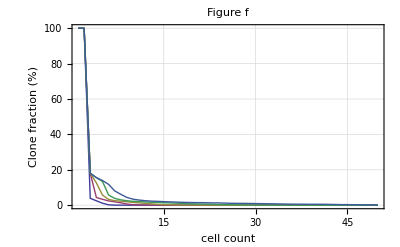

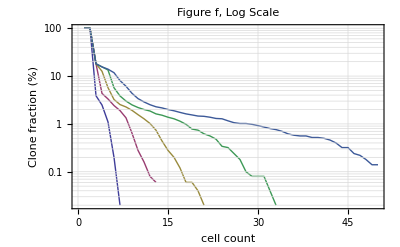

```mathematica
ListLinePlot[cumulativewithsinglets2D,PlotRange->All,PlotLabel->"Figure f",Frame->True,GridLines->Automatic,FrameLabel->{"cell count","Clone fraction (%)"}]
ListLogPlot[cumulativewithsinglets2D,PlotRange->All,Joined->True,PlotLabel->"Figure f, Log Scale",GridLines->Automatic,Frame->True,FrameLabel->{"cell count","Clone fraction (%)"}]
```

## Animate

```mathematica
anim=ListAnimate[output]
```

```mathematica
Export["~/Desktop/cellgrowth.swf",output]
```

~/Desktop/cellgrowth.swf